# Small V

## General definitions

### Base quantities

```mathematica
ClearAll[coordsU];
coordsU={t,x,y,z};

ClearAll[vU];
vU={vx[t,x,y,z],vy[t,x,y,z],vz[t,x,y,z]};

ClearAll[gUU];
gUU=α[t,x,y,z]^(-2){
{-1,-vU[[1]],-vU[[2]],-vU[[3]]},
{-vU[[1]],α[t,x,y,z]^2-vU[[1]]vU[[1]],-vU[[1]]vU[[2]],-vU[[1]]vU[[3]]},
{-vU[[2]],-vU[[2]]vU[[1]],α[t,x,y,z]^2-vU[[2]]vU[[2]],-vU[[2]]vU[[3]]},
{-vU[[3]],-vU[[3]]vU[[1]],-vU[[3]]vU[[2]],α[t,x,y,z]^2-vU[[3]]vU[[3]]}
}//FullSimplify;

ClearAll[gLL];
gLL=FullSimplify[Inverse[gUU]];
```

### ADM quantities

```mathematica
ClearAll[scoordsU];
scoordsU=coordsU[[2;;4]];

ClearAll[γLL,γUU];
γLL=gLL[[2;;4,2;;4]];
γUU=FullSimplify[Inverse[γLL]];

ClearAll[lapse];
lapse=Simplify[Sqrt[-1/gUU[[1,1]]],α[t,x,y,z]>=0];

ClearAll[βU,βL];
βU=gUU[[1,2;;4]]α[t,x,y,z]^2;
βL=gLL[[1,2;;4]];

ClearAll[KLL];
KLL=Table[
1/(2lapse)(D[βL[[j]],scoordsU[[i]]]+D[βL[[i]],scoordsU[[j]]]),
{i,1,3},
{j,1,3}
]//FullSimplify;

ClearAll[nU,nL];
nU=Join[{1/lapse},-βU/lapse];
nL=FullSimplify[Table[Sum[gLL[[a,b]]nU[[b]],{b,1,4}],{a,1,4}]];
```

### 4-Christoffel symbols

```mathematica
ClearAll[Γ];
Γ=Table[
FullSimplify[
(1/2)*Sum[
(gUU[[i,s]])*(D[gLL[[s,j]],coordsU[[k]] ]+D[gLL[[s,k]],coordsU[[j]] ]-D[gLL[[j,k]],coordsU[[s]] ]),
{s,1,4}
]
],
{i,1,4},
{j,1,4},
{k,1,4}
] ;
```

### Geodesic equation checker

Compute the geodesic equations from a 4-velocity vector

```mathematica
ClearAll[geodesicEquations]
geodesicEquations[velU_,velL_]:=FullSimplify[
Table[
Sum[velU[[a]]D[velL[[b]],coordsU[[a]]],{a,1,4}]
-Sum[velU[[a]]Γ[[i,a,b]]velL[[i]],{i,1,4},{a,1,4}],
{b,1,4}
]
];
```

### Vincent geodesic equations

```mathematica
ClearAll[VU];
VU={velx,vely,velz};

ClearAll[dXudt];
dXudt=FullSimplify[
Table[
lapse*VU[[i]]-βU[[i]],
{i,1,3}
]
];

ClearAll[dVUdt];
dVUdt=FullSimplify[
Table[
Sum[lapse*VU[[j]]VU[[i]]D[Log[lapse],scoordsU[[j]]],{j,1,3}]
-Sum[lapse*VU[[j]]VU[[i]]KLL[[j,k]]VU[[k]],{j,1,3},{k,1,3}]
+2Sum[lapse*VU[[j]]γUU[[i,k]]KLL[[k,j]],{k,1,3},{j,1,3}]
-Sum[γUU[[i,j]]D[lapse,scoordsU[[j]]],{j,1,3}]
-Sum[VU[[j]]D[βU[[i]],scoordsU[[j]]],{j,1,3}]
,
{i,1,3}
]
];

ClearAll[dEdt];
dEdt=FullSimplify[
energy(Sum[lapse*KLL[[j,k]]VU[[j]]VU[[k]],{j,1,3},{k,1,3}]-Sum[VU[[j]]D[lapse,scoordsU[[j]]],{j,1,3}])
];
```

### Restricting to Alcubierre

```mathematica
ClearAll[r];
r[t_,x_,y_,z_]:=Sqrt[(x-u*t)^2+y^2+z^2];

ClearAll[α,vx,vy,vz];
α[t_,x_,y_,z_]:=1;
vx[t_,x_,y_,z_]:=u*f[r[t,x,y,z]];
vy[t_,x_,y_,z_]:=0;
vz[t_,x_,y_,z_]:=0;
```

### Transition

```mathematica
ClearAll[deg,poly];
deg=1;
poly[x_]:=Sum[c[i]x^i,{i,0,deg}];

ClearAll[polyCs];
polyCs=Solve[
{
poly[x0]==y0,
poly[x0+dx]==yf
},
Table[c[i],{i,0,deg}]
]//Flatten//FullSimplify;

ClearAll[polyWithCs];
polyWithCs=FullSimplify[poly[x]//.polyCs]

ClearAll[polyTrans];
polyTrans[x_,y0_,yf_,x0_,dx_]:=Piecewise[
{
{y0,x<x0},
{yf,x>(x0+dx)},
{y0-((x-x0) (y0-yf))/dx,True}
}
]

polyTrans[x_,x0_,dx_]:=polyTrans[x,1,0,x0,dx];
```

y0-((x-x0) (y0-yf))/dx

```mathematica
D[polyTrans[x,y0,yf,x0,dx],x]//FullSimplify
```

Piecewise[{{0, x<x0||dx+x0<x}, {(-y0+yf)/dx, True}}]

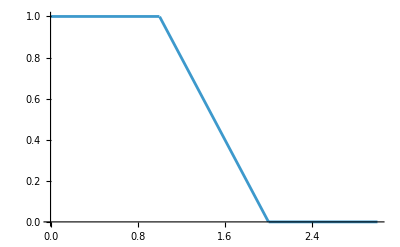

```mathematica
Plot[polyTrans[x,1,1],{x,0,3}]
```

```mathematica
FullSimplify[polyTrans[x,radius,sigma]]
```

Piecewise[{{1, x<radius}, {0, x>radius+sigma}, {(radius+sigma-x)/sigma, True}}]

## V and p correspondence

We know that the normal vector is a solution to the geodesic equation

```mathematica
geodesicEquations[nU,nL]
```

{0,0,0,0}

How we translate this normal vector to V? We use Vincent equation (8)
Suppose that we have Vx = Vy = Vz = 0

```mathematica
FullSimplify[energy(nU+Join[{0},VU])//.{velx->0,vely->0,velz->0}]
```

{energy,energy u f[√((-t u+x)^2+y^2+z^2)],0,0}

Note that this is nU if energy = 1

```mathematica
nU
```

{1,u f[√((-t u+x)^2+y^2+z^2)],0,0}

So a particle with Vx = Vy = Vz = 0 and E = 1 follows a geodesic trajectory.
Under these conditions, dE/dt = 0

```mathematica
dEdt//.{velx->0,vely->0,velz->0}
```

0

## Perturbation

We now know that choosing Vx = Vy = Vz = 0 and E = 1 is equivalent to choosing a particle with 4-momentum nU
We also know that a curve q^μ(λ) with tangent vector nU satisfies the geodesic equation (and thus is a geodesic)

```mathematica
{t'[λ],x'[λ],y'[λ],z'[λ]}==nU
```

{t'[λ],x'[λ],y'[λ],z'[λ]}=={1,u f[√((-t u+x)^2+y^2+z^2)],0,0}

What is the 4-momentum of a particle with velocity Vx = ϵ, Vy = Vz = 0 and E such that the 4-vector is normalized?

```mathematica
FullSimplify[(nU+{0,ϵ,0,0})/Sqrt[1-ϵ^2]]
```

{1/(√(1-ϵ^2)),(ϵ+u f[√((-t u+x)^2+y^2+z^2)])/(√(1-ϵ^2)),0,0}

We can show it is normalized

```mathematica
ClearAll[vecL];
vecU=FullSimplify[(nU+{0,ϵ,0,0})/Sqrt[1-ϵ^2]];
Print["Normalized? ",FullSimplify[Sum[gLL[[a,b]]vecU[[a]]vecU[[b]],{a,1,4},{b,1,4}]==-1]]
ClearAll[vecL];
```

Normalized? True

The geodesic equations are

```mathematica
FullSimplify[dXudt//.{velx->ϵ,vely->0,velz->0}]
FullSimplify[dVUdt//.{velx->ϵ,vely->0,velz->0}]
FullSimplify[dEdt//.{velx->ϵ,vely->0,velz->0,energy->1/Sqrt[1-ϵ^2]}]
```

{ϵ+u f[√((-t u+x)^2+y^2+z^2)],0,0}

{-(u (t u-x) ϵ (-1+ϵ^2) f'[√((-t u+x)^2+y^2+z^2)])/(√((-t u+x)^2+y^2+z^2)),-(u y ϵ f'[√((-t u+x)^2+y^2+z^2)])/(√((-t u+x)^2+y^2+z^2)),-(u z ϵ f'[√((-t u+x)^2+y^2+z^2)])/(√((-t u+x)^2+y^2+z^2))}

(u (t u-x) ϵ^2 f'[√((-t u+x)^2+y^2+z^2)])/(√((-t u+x)^2+y^2+z^2) √(1-ϵ^2))

From dXudt, we can see that if we choose y[0]=z[0]=0, we never deviate from the x line and get

```mathematica
FullSimplify[dXudt//.{velx->ϵ,vely->0,velz->0,y->0,z->0}]
FullSimplify[dVUdt//.{velx->ϵ,vely->0,velz->0,y->0,z->0}]
FullSimplify[dEdt//.{velx->ϵ,vely->0,velz->0,y->0,z->0,energy->1/Sqrt[1-ϵ^2]}]
```

{ϵ+u f[√((-t u+x)^2)],0,0}

{-(u (t u-x) ϵ (-1+ϵ^2) f'[√((-t u+x)^2)])/(√((-t u+x)^2)),0,0}

(u (t u-x) ϵ^2 f'[√((-t u+x)^2)])/(√((-t u+x)^2) √(1-ϵ^2))

If we solve the ODE for a time domain where x>=ut,t<=x/u
This means that

```mathematica
FullSimplify[ϵ+u f[√((-t u+x)^2)],{x>=u*t}]
FullSimplify[-(u (t u-x) ϵ (-1+ϵ^2) f'[√((-t u+x)^2)])/(√((-t u+x)^2)),{x>=u*t}]
FullSimplify[(u (t u-x) ϵ^2 f'[√((-t u+x)^2)])/(√((-t u+x)^2) √(1-ϵ^2)),{x>=u*t}]
```

ϵ+u f[-t u+x]

u ϵ (-1+ϵ^2) f'[-t u+x]

-(u ϵ^2 f'[-t u+x])/(√(1-ϵ^2))

```mathematica
ClearAll[f];
f[x_]:=(radius+sigma-x)/sigma;

(* 
ξ = x-u t
x = ξ+u t
dx/dt = dξ/dt+u
*)
ClearAll[eqs];
eqs=FullSimplify[{x'[t]==ϵ+u f[-t u+x[t]],Vx'[t]==u ϵ (-1+ϵ^2) f'[-t u+x[t]],x[0]==x0,Vx[0]==vx0}];

DSolve[eqs,{x[t],Vx[t]},t]//FullSimplify

ClearAll[f];
ClearAll[eqs];
```

{{x[t]→radius+t u+(sigma ϵ)/u-(ⅇ^(-(t u)/sigma) (radius u-u x0+sigma ϵ))/u,Vx[t]→(sigma vx0+t u ϵ-t u ϵ^3)/sigma}}